```mathematica
m:=20000;V:=100;g:=9.8;p:=1000;v0:=10;k:=1.5;H0:=100;a=25;p0=250000;H1=90;c:=m*g-p*g*V;
```

```mathematica
sol=NDSolve[{-m*u'[t]==c+k*(u[t])^(1.75),u[0]==v0},u[t],{t,0,5}]
```

{{u[t]→InterpolatingFunction[{{0., 5.}}, <>][t]}}

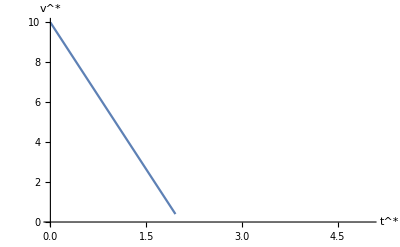

```mathematica
Plot[u[t]/.sol,{t,0,5},AxesLabel->{SuperStar[t],SuperStar[v]}]
```

```mathematica
solh=NDSolve[{-m*v[h]*v'[h]==c+k*(v[h])^(1.75)-p0+a*h,v[-90]==5},v[h],{h,-90,5}]
```

{{v[h]→InterpolatingFunction[{{-90., 5.}}, <>][h]}}

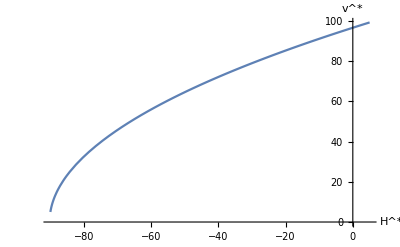

```mathematica
Plot[v[h]/.solh,{h,-90,5},AxesLabel->{SuperStar[H],SuperStar[v]}]
```

```mathematica
solhv=NDSolve[{-h'[u]==u*m/(c+k*(u)^(1.75)),h[v0]==-H0},h[u],{u,0,10}]
```

{{h[u]→InterpolatingFunction[{{0., 10.}}, <>][u]}}

InterpolatingFunction::dmval: Input value {-9.99959} lies outside the range of data in the interpolating function. Extrapolation will be used.

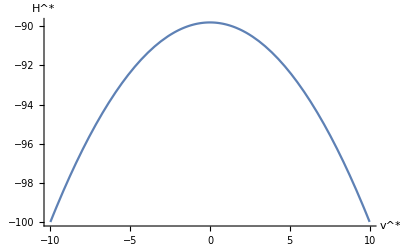

```mathematica
Plot[h[u]/.solhv,{u,-10,10},AxesLabel->{SuperStar[v],SuperStar[H]}]
```

```mathematica
sol=NDSolve[{m*u''[t]==c+k*(u'[t])^(1.75)-p0+a*u[t],u'[2]==-5,u[2]==90},u[t],{t,0,5}]
```

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument 20000 SuperscriptBox[SuperscriptBox[True.

NDSolve[{20000 u''[t]==-152000.+25 u[t]+1.5 u'[t]^1.75,u'[2]==-5,True},u[t],{t,0,5}]